# Differential Equations for Cosmological Correlators

## Nima Arkani-Hamed, Daniel Baumann, Aaron Hillman, Austin Joyce, Hayden Lee, and Guilherme Pimentel

This notebook contains details of the differential equations for the two-site chain.

```mathematica
SetDirectory[NotebookDirectory[]];
<<kinematic-flow.wl
```

## 2-site chain

### Definitions

```mathematica
nsite=2;
```

Projective planes:

```mathematica
X={x1,x2,1};
P[1]={1,0,X1+Y};
P[2]={0,1,X2+Y};
P[3]={1,1,X1+X2};

P[4]={1,0,0};
P[5]={0,1,0};
L[i_]:=P[i].X
planes=Table[L[i],{i,5}]
```

{x1+X1+Y,x2+X2+Y,x1+X1+x2+X2,x1,x2}

Generate letters:

```mathematica
planes[[;;3]]/.x1->0/.x2->0;
Ysub=Subsets[{Y},2]/.Y->(Y->-Y);
letters=Table[%%/.Ysub[[i]],{i,Length@Ysub}]//Flatten//DeleteDuplicates//Sort
flip=Table[Rule[{#1[[i]]},{#2[[i]]}]&[-letters,letters],{i,Length@letters}];
logs=Log/@letters;
```

{X1+X2,X1-Y,X2-Y,X1+Y,X2+Y}

### Basis functions

#### Function tree

Function labels:

```mathematica
list=Flatten[Table[Subsets[{1,2},3],{i,2}],1]//DeleteDuplicates
nn=Cases[list//Sort,#]&/@Table[_,{i,0,2},{j,i}];
```

{{},{1},{2},{1,2}}

Tree structure and the number of functions in each twist layer:

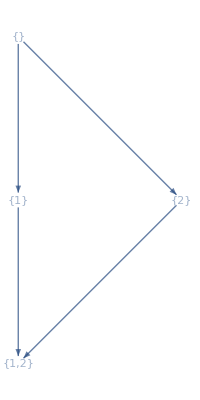

# twists | 0 | 1 | 2
# functions | 1 | 2 | 1

```mathematica
funcTree@list
```

#### Twist replacements

Replacement operation at each vertex:

```mathematica
rr[1][f_]:=replace[1,4]@f
rr[2][f_]:=replace[2,5]@f
```

Wavefunction:

```mathematica
ψ=⟨1,2⟩+⟨2,3⟩+⟨3,1⟩;
```

Generate basis functions:

```mathematica
Subscript[f, {}]==(Subscript[F, {}]=ψ)

Table[Subscript[f, nn[[2]][[j]]]==(Subscript[F, nn[[2]][[j]]]=ψ//rr[nn[[2]][[j]][[1]]]),{j,Length@nn[[2]]}]//Column

Table[Subscript[f, nn[[3]][[j]]]==(Subscript[F, nn[[3]][[j]]]=ψ//rr[nn[[3]][[j]][[1]]]//rr[nn[[3]][[j]][[2]]]),{j,Length@nn[[3]]}]//Column
```

f_{}==⟨1,2⟩+⟨2,3⟩+⟨3,1⟩

f_{1}==⟨2,3⟩-⟨2,4⟩+⟨3,4⟩
f_{2}==-⟨1,3⟩+⟨1,5⟩-⟨3,5⟩

f_{1,2}==⟨3,4⟩-⟨3,5⟩+⟨4,5⟩

### Differential equations

```mathematica
solveCoeff;
fsub={Subscript[f, {}]->"ψ",Subscript[f, {1}]->"F",Subscript[f, {2}]->"F̃",Subscript[f, {1,2}]->"Z"};
```

```mathematica
dfeq=Flatten@Table[eqlvl[l][[m]],{l,3},{m,Length@nn[[l]]}];
dfeq/.fsub//Column
```

d[ψ]==F dL_(X1-Y)+F̃ dL_(X2-Y)+(-F+ψ) dL_(X1+Y)+(-F̃+ψ) dL_(X2+Y)
d[F]==Z dL_(X1+X2)+F dL_(X1-Y)+(F-Z) dL_(X2+Y)
d[F̃]==Z dL_(X1+X2)+F̃ dL_(X2-Y)+(F̃-Z) dL_(X1+Y)
d[Z]==2 Z dL_(X1+X2)

### A matrix

```mathematica
nsite=2;
flist=Flatten[Table[Subscript[f, nn[[l]][[m]]],{l,nsite+1},{m,Length@nn[[l]]}],1];
```

```mathematica
Flatten[Table[eqlvl[i][[m]][[2]],{i,0,nsite+1},{m,Length@eqlvl[i]}],1];
Amtx=Table[Coefficient[%[[i]],flist],{i,4^(nsite-1)}];
```

```mathematica
Amtx//MatrixForm
```

(dL_(X1+Y)+dL_(X2+Y) | dL_(X1-Y)-dL_(X1+Y) | dL_(X2-Y)-dL_(X2+Y) | 0
0 | dL_(X1-Y)+dL_(X2+Y) | 0 | dL_(X1+X2)-dL_(X2+Y)
0 | 0 | dL_(X2-Y)+dL_(X1+Y) | dL_(X1+X2)-dL_(X1+Y)
0 | 0 | 0 | 2 dL_(X1+X2))

Check flatness:

```mathematica
A=Amtx/.Subscript[dL, a_]:>Dt@Log[a];
vars={X1,X2,Y};
DeleteDuplicates@Flatten@Table[Coefficient[A,Dt[vars[[i]]]].Coefficient[A,Dt[vars[[j]]]]-Coefficient[A,Dt[vars[[j]]]].Coefficient[A,Dt[vars[[i]]]]//Simplify,{i,Length@vars},{j,Length@vars}]
```

{0}

### d^2=0

Generate 3-letter relations:

```mathematica
DeleteDuplicates@DeleteCases[Flatten[Table[If[(Subscript[dL, letters[[i]]]⋀Subscript[dL, letters[[k]]]+Subscript[dL, letters[[j]]]⋀Subscript[dL, letters[[i]]]-Subscript[dL, letters[[j]]]⋀Subscript[dL, letters[[k]]]/.Subscript[dL, x_]:>Dt@Log@x/.Dt->dL/.Dt->dL/.dL[a_]:>Subscript[dL, a]//dLsimp)===0∧i=!=j∧i=!=k∧j=!=k,{i,j,k},0],{i,Length@letters},{j,Length@letters},{k,Length@letters}],2],0];
reltab=Subscript[dL, letters[[#1]]]⋀Subscript[dL, letters[[#3]]]+Subscript[dL, letters[[#2]]]⋀Subscript[dL, letters[[#1]]]-Subscript[dL, letters[[#2]]]⋀Subscript[dL, letters[[#3]]]&@@@%//dLsimp;
```

Independent relations:

```mathematica
dLrel=Table[If[reltab[[i,1]][[1]]===-1,-reltab[[i]],reltab[[i]]],{i,Length@reltab}]//DeleteDuplicates
dLsub=Table[%[[i]][[1]]->-%[[i]][[2]]-%[[i]][[3]],{i,Length@%}];
dLsub=Table[dLrel[[i]][[1]]->Subscript[R, i]-dLrel[[i]][[2]]-dLrel[[i]][[3]],{i,Length@dLrel}];
%//Length
```

{dL_(X1+X2)⋀dL_(X1-Y)-dL_(X1+X2)⋀dL_(X2+Y)+dL_(X1-Y)⋀dL_(X2+Y),dL_(X1+X2)⋀dL_(X2-Y)-dL_(X1+X2)⋀dL_(X1+Y)+dL_(X2-Y)⋀dL_(X1+Y)}

2

Taking d^2:

```mathematica
dfsub=dfeq/.a_==b_:>a->b;
ddeq=Flatten@Table[d[Subscript[f, nn[[l]][[m]]]],{l,3},{m,Length@nn[[l]]}]/.d[f_]:>(d^2)[f]==dd[f];
```

Substituting three-letter relations:

```mathematica
ddeq/.dLsub/.fsub//Simplify//Column
```

d^2[ψ]==Z (R_1+R_2)
d^2[F]==Z R_1
d^2[F̃]==Z R_2
d^2[Z]==0

### Symbol

A matrix in the dS limit:

```mathematica
flist2=flist/.Subscript[f, a_]:>ϵ^(-Length@a)Subscript[f, a];
Series[ϵ (Amtx.flist2)/(flist2/.Subscript[f, __]->1),{ϵ,0,0}]//Normal;
Amtxeps0=Table[Coefficient[%[[i]],flist],{i,4^(nsite-1)}];
Amtxeps0//MatrixForm
```

(0 | dL_(X1-Y)-dL_(X1+Y) | dL_(X2-Y)-dL_(X2+Y) | 0
0 | 0 | 0 | dL_(X1+X2)-dL_(X2+Y)
0 | 0 | 0 | dL_(X1+X2)-dL_(X1+Y)
0 | 0 | 0 | 0)

Symbol from differential equations:

```mathematica
Sym3=S/@flist;
Amtxeps0.flist/.Subscript[dL, a_]:>dLog[a]/.dLog[a_]-dLog[b_]:>dLog[a/b]/.Subscript[f, {1,2}]:>1;
A3eq=%/.Subscript[f, a_] dLog[x_]:>S[Subscript[f, a]]⊗x/. dLog[x_]:>x;
Symrule=Table[Sym3[[i]]->%[[i]],{i,4}];
```

```mathematica
Sdiff=A3eq[[1]]//.Symrule//TensorSimp
```

(X1+X2)/(X1+Y)⊗(X2-Y)/(X2+Y)+(X1+X2)/(X2+Y)⊗(X1-Y)/(X1+Y)